## Мухамадиев Владимир

# Задание 6

## Загрузка и предварительная обработка

```mathematica
data1=Import[NotebookDirectory[]<>"\\bio-yeast.txt","Data"];
```

```mathematica
el1=Table[data1⟦i,1⟧<->data1⟦i,2⟧,{i,1,Length[data1]}];
```

```mathematica
g1=Graph[el1];
```

```mathematica
data2=Import[NotebookDirectory[]<>"\\ca-netscience.txt","Data"];
```

```mathematica
el2=Table[data2⟦i,1⟧<->data2⟦i,2⟧,{i,1,Length[data2]}];
```

```mathematica
g2=Graph[el2];
```

```mathematica
data3=Import[NotebookDirectory[]<>"\\proteins.txt","Data"];
```

```mathematica
el3=Table[data3⟦i,1⟧<->data3⟦i,2⟧,{i,1,Length[data3]}];
```

```mathematica
g3=Graph[el3];
```

## 1. Матрица корреляций степеней вершин

### Матрица корреляций степеней вершин заданного графа

```mathematica
DegreeCorrelationMatrix[graph_]:=Module[{el=EdgeList[graph],ec=EdgeCount[graph]},Divide[Normal[SparseArray[Normal[Counts[Partition[Flatten[{Table[{VertexDegree[graph,el⟦i,1⟧],VertexDegree[graph,el⟦i,2⟧]},{i,1,ec}],Table[{VertexDegree[graph,el⟦i,2⟧],VertexDegree[graph,el⟦i,1⟧]},{i,1,ec}]}],2]]]]],2ec]]
```

### Визуализация матрицы корреляций степеней вершин заданного графа

```mathematica
DegreeCorrelationMatrixPlot[graph_,zeros_]:=If[zeros==True,MatrixPlot[DegreeCorrelationMatrix[graph],DataReversed->{True,False},PlotLegends->Automatic],MatrixPlot[DeleteCases[DeleteCases[DegreeCorrelationMatrix[graph],{0..}]ᵀ,{0..}]ᵀ,DataReversed->{True,False},FrameTicks->None,PlotLegends->Automatic]]
```

### Коэффициент ассортативности по заданной матрице корреляций степеней вершин графа

```mathematica
AssortativityCoefficient[mat_]:=Module[{n=Length[mat]},(∑_(i=1)^n ∑_(j=1)^n i j(mat⟦i,j⟧-(∑_(j=1)^n mat⟦i,j⟧)∑_(i=1)^n mat⟦j,i⟧))/(∑_(i=1)^n i^2∑_(j=1)^n mat⟦i,j⟧-(∑_(i=1)^n i∑_(j=1)^n mat⟦i,j⟧)^2)]
```

### Для заданных графов

#### bio-yeast

```mathematica
DegreeCorrelationMatrixPlot[g1,True]
```

-Graphics-

```mathematica
DegreeCorrelationMatrixPlot[g1,False]
```

-Graphics-

```mathematica
N[AssortativityCoefficient[DegreeCorrelationMatrix[g1]]]
```

-0.209541

```mathematica
N[GraphAssortativity[g1]]
```

-0.209541

#### ca-netscience

```mathematica
DegreeCorrelationMatrixPlot[g2,True]
```

-Graphics-

```mathematica
DegreeCorrelationMatrixPlot[g2,False]
```

-Graphics-

```mathematica
N[AssortativityCoefficient[DegreeCorrelationMatrix[g2]]]
```

-0.0816778

```mathematica
N[GraphAssortativity[g2]]
```

-0.0816778

#### proteins

```mathematica
DegreeCorrelationMatrixPlot[g3,True]
```

-Graphics-

```mathematica
DegreeCorrelationMatrixPlot[g3,False]
```

-Graphics-

```mathematica
N[AssortativityCoefficient[DegreeCorrelationMatrix[g3]]]
```

0.396777

```mathematica
N[GraphAssortativity[g3]]
```

0.396777

## 2. Функция корреляции степеней

### Аппроксимация в двойном логарифмическом масштабе функции средней степени соседа по степеням по заданному графу

```mathematica
MDCLA[graph_]:=Module[{data=Log[DeleteCases[{Range[Max[VertexDegree[graph]]],MeanDegreeConnectivity[graph]⟦2;;-1⟧}ᵀ,{_,0}]]},Show[ListPlot[data,PlotStyle->Red],Plot[Evaluate[Normal[LinearModelFit[data,x,x]]],{x,0,Max[data]},PlotLegends->"AllExpressions"]]]
```

### Для заданных графов

#### bio-yeast

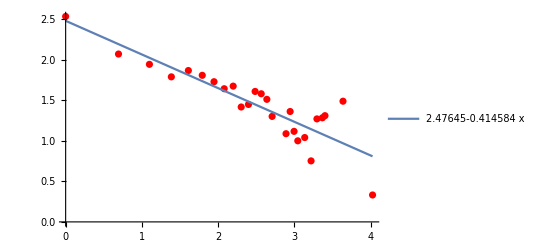

```mathematica
MDCLA[g1]
```

#### ca-netscience

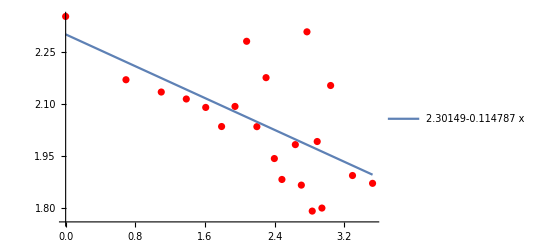

```mathematica
MDCLA[g2]
```

#### proteins

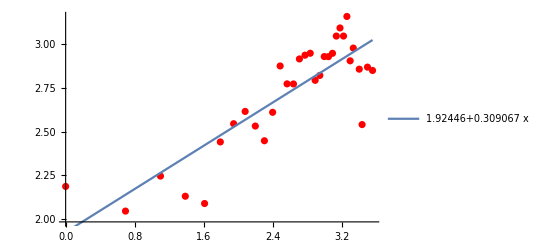

```mathematica
MDCLA[g3]
```

## 3. Алгоритм Xalvi-Brunet & Sokolov

### Функция которая приводит список ребер к виду, где в каждом ребре v_1<->v_2,v_1≤v_2

```mathematica
EdgeSort[edgelist_]:=Module[{out=edgelist},Do[If[edgelist⟦i,1⟧>edgelist⟦i,2⟧,out⟦i⟧=edgelist⟦i,2⟧<->edgelist⟦i,1⟧],{i,1,Length[edgelist]}];out]
```

### Рандомизация графа которая не создает новых петель и мультиребер и приводит к ассортативному/дисассортативному виду

```mathematica
GraphRandomizationByAssortativity[g_,n_,assortativity_]:=Module[{el=EdgeSort[EdgeList[g]],eltemp={},vltemp={},temp={{},{}},v={},vd={},k=0},Do[temp⟦1⟧=RandomChoice[el](*Выбираем первое ребро/петлю*);eltemp=DeleteCases[el,temp⟦1⟧](*Создаем временную выборку из ребер/петель и удалаем из нее все мультиребра/мультипетли для выбранного ребра/петли*);If[temp⟦1,1⟧==temp⟦1,2⟧,(*Алгоритм выбрал петлю*)eltemp=DeleteCases[eltemp,v_<->v_](*удаляем из временной выбрки все петли*);vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранная петля*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данной петлей*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал петлю которую нельзя изменить, так как до любой вершины из нее можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро*)],(*Алгоритм выбрал ребро*)vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧],Cases[eltemp,temp⟦1,2⟧<->_],Cases[eltemp,_<->temp⟦1,2⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранное ребро*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данным ребром*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал ребро которое нельзя изменить, так как до любой вершины из него можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро/петлю*)]];v={temp⟦1,1⟧,temp⟦1,2⟧,temp⟦2,1⟧,temp⟦2,2⟧}(*Вершины выбранных ребер*);vd={VertexDegree[g,temp⟦1,1⟧],VertexDegree[g,temp⟦1,2⟧],VertexDegree[g,temp⟦2,1⟧],VertexDegree[g,temp⟦2,2⟧]}(*Степени вершин выбранных ребер*);If[Length[DeleteDuplicates[vd]]==1,Goto[end](*Все степени вершин у выбранных ребер совпали, при переключении ассортативность не изменится. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*)];k=1;While[(el⟦k⟧===temp⟦1⟧)==False,k++];el=Delete[el,k];k=1;While[(el⟦k⟧===temp⟦2⟧)==False,k++];el=Delete[el,k](*Удаляем из списка ребер выбранные*);If[assortativity==True,temp=ReverseSortBy[{{EdgeSort[{v⟦1⟧<->v⟦2⟧,v⟦3⟧<->v⟦4⟧}],Correlation[{vd⟦1⟧,vd⟦2⟧,vd⟦3⟧,vd⟦4⟧},{vd⟦2⟧,vd⟦1⟧,vd⟦4⟧,vd⟦3⟧}]},{EdgeSort[{v⟦1⟧<->v⟦3⟧,v⟦2⟧<->v⟦4⟧}],Correlation[{vd⟦1⟧,vd⟦3⟧,vd⟦2⟧,vd⟦4⟧},{vd⟦3⟧,vd⟦1⟧,vd⟦4⟧,vd⟦2⟧}]},{EdgeSort[{v⟦1⟧<->v⟦4⟧,v⟦2⟧<->v⟦3⟧}],Correlation[{vd⟦1⟧,vd⟦4⟧,vd⟦2⟧,vd⟦3⟧},{vd⟦4⟧,vd⟦1⟧,vd⟦3⟧,vd⟦2⟧}]}},Last]⟦1,1⟧(*Выбор переключения дающий наибольшую ассортативность*),temp=SortBy[{{EdgeSort[{v⟦1⟧<->v⟦2⟧,v⟦3⟧<->v⟦4⟧}],Correlation[{vd⟦1⟧,vd⟦2⟧,vd⟦3⟧,vd⟦4⟧},{vd⟦2⟧,vd⟦1⟧,vd⟦4⟧,vd⟦3⟧}]},{EdgeSort[{v⟦1⟧<->v⟦3⟧,v⟦2⟧<->v⟦4⟧}],Correlation[{vd⟦1⟧,vd⟦3⟧,vd⟦2⟧,vd⟦4⟧},{vd⟦3⟧,vd⟦1⟧,vd⟦4⟧,vd⟦2⟧}]},{EdgeSort[{v⟦1⟧<->v⟦4⟧,v⟦2⟧<->v⟦3⟧}],Correlation[{vd⟦1⟧,vd⟦4⟧,vd⟦2⟧,vd⟦3⟧},{vd⟦4⟧,vd⟦1⟧,vd⟦3⟧,vd⟦2⟧}]}},Last]⟦1,1⟧(*Выбор переключения дающий наибольшую дисассортативность*)];AppendTo[el,temp⟦1⟧];AppendTo[el,temp⟦2⟧](*Добавляем новые ребра*);Label[end],{i,1,n}];Graph[el]]
```

### Работа алгоритма рандомизации на примере графа bio-yeast

#### Изначальный граф

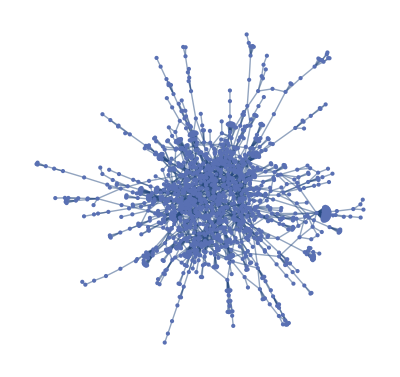

```mathematica
g1
```

```mathematica
N[GraphAssortativity[g1]]
```

-0.209541

#### Граф после ассортативной рандомизации

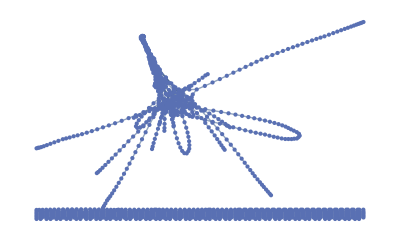

```mathematica
g1a=Import[NotebookDirectory[]<>"//g1a.m"](*g1a=GraphRandomizationByAssortativity[g1,100000,True]*)
```

```mathematica
N[GraphAssortativity[g1a]]
```

0.570559

#### Граф после дисассортативной рандомизации

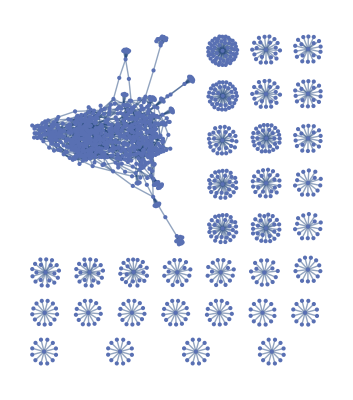

```mathematica
g1d=Import[NotebookDirectory[]<>"//g1d.m"](*g1d=GraphRandomizationByAssortativity[g1,100000,False]*)
```

```mathematica
N[GraphAssortativity[g1d]]
```

-0.386286

### Генерация случайного графа Эрдеша-Реньи по заданному числу вершин и вероятности появления ребра

```mathematica
ErdősRenyiGraph[n_,p_]:=Graph[Flatten[Table[RandomChoice[{p,1-p}->{i<->j,{}}],{i,1,n-1},{j,i+1,n}]]]
```

### Работа алгоритма рандомизации на примере случайного графа

#### Изначальный граф

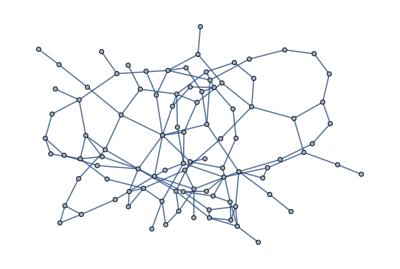

```mathematica
rg=ErdősRenyiGraph[100,1/40]
```

```mathematica
N[GraphAssortativity[rg]]
```

0.062069

#### Граф после ассортативной рандомизации

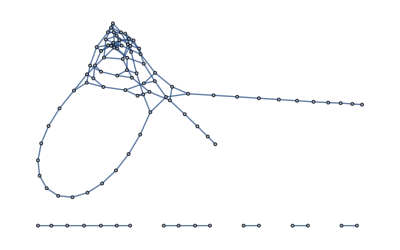

```mathematica
rga=GraphRandomizationByAssortativity[rg,1000,True]
```

```mathematica
N[GraphAssortativity[rga]]
```

0.758818

#### Граф после дисассортативной рандомизации

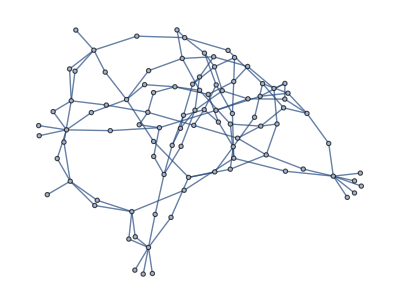

```mathematica
rgd=GraphRandomizationByAssortativity[rg,1000,False]
```

```mathematica
N[GraphAssortativity[rgd]]
```

-0.798818

### Специальная функция. Создает заданное количество графов Эрдеша-Реньи с заданными параметрами. С каждым графом производится ассортативная и дисассортативная рандомизация с заданным числом шагов. На выходе три числа: средний размер главной компоненты у дисассортативных, исходных и ассортативных графов.

```mathematica
SF[n_,p_,na_,nr_]:=Module[{gp=Table[ErdősRenyiGraph[n,p],{i,1,na}],ga={},gd={},out={}},ga=Table[GraphRandomizationByAssortativity[gp⟦i⟧,nr,True],{i,1,na}];gd=Table[GraphRandomizationByAssortativity[gp⟦i⟧,nr,False],{i,1,na}];out={Mean[Table[VertexCount[ConnectedGraphComponents[gd⟦i⟧]⟦1⟧],{i,1,na}]],Mean[Table[VertexCount[ConnectedGraphComponents[gp⟦i⟧]⟦1⟧],{i,1,na}]],Mean[Table[VertexCount[ConnectedGraphComponents[ga⟦i⟧]⟦1⟧],{i,1,na}]]};out]
```

```mathematica
sim1000=Import[NotebookDirectory[]<>"//sim1000.m"];(*sim1000=Table[SF[1000,l,100,1000],{l,10^-4,5 10^-3,10^-4}];*)
```

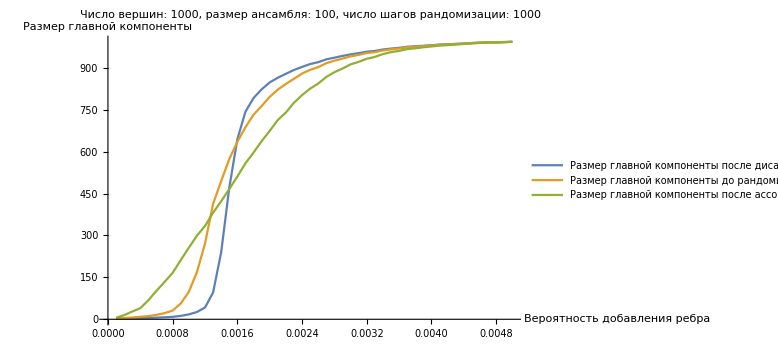

```mathematica
ListLinePlot[{{Range[10^-4,5 10^-3,10^-4],sim1000⟦All,1⟧}ᵀ,{Range[10^-4,5 10^-3,10^-4],sim1000⟦All,2⟧}ᵀ,{Range[10^-4,5 10^-3,10^-4],sim1000⟦All,3⟧}ᵀ},PlotLabel->"Число вершин: 1000, размер ансамбля: 100, число шагов рандомизации: 1000",AxesLabel->{"Вероятность\nдобавления\nребра","Размер главной\nкомпоненты"},ImageSize->Large,PlotLegends->Placed[{"Размер главной компоненты после дисассортативной рандомизации","Размер главной компоненты до рандомизации","Размер главной компоненты после ассортативной рандомизации"},Below]]
```